```mathematica
ClearAll[df1,df2,f];
f[w1_,w2_,x_,a_,b_,m_]:=w1 x^b+w2 x(1-(1-x^(a-1))^m)(1-w1 x^b);
df1[w1_,w2_,x_,a_,b_,m_]:=x^b(1-w2 x(1-(1-x^(a-1))^m));
df2[w1_,w2_,x_,a_,b_,m_] := x(1-(1-x^(a-1))^m)(1-w1 x^b);
(*Plot3D[df1[x,y,0.5,3,2,2],{x,0,1},{y,0,1}]*)
(*Grad[f[w1,w2,0.5,3,2,2],{w1,w2}]*)
(*VectorPlot[Grad[f[w1,w2,0.5,3,2,2],{w1,w2}],{w1,0,1},{w2,0,1}]*)
```

```mathematica
f1[x_,y_,z_]:=z(1-y z(1-(1-z^2)^2));
f2[x_,y_,z_]:=z(1-(1-z^2)^2)(1-x z);
VectorPlot[{df1[x,y,z,3,2,2],df2[x,y,0.5,3,2,2]},{x,0,1},{y,0,1},{z,0,1}]
```

```mathematica
a1=3;
b1=2;
m1=5;
z=0.9;
Table[Show[{ContourPlot[f[x,y,z,a1,b1,m1],{x,0,1},{y,0,1},ContourLabels->True],
VectorPlot[{{df1[x,y,z,a1,b1,m1],df2[x,y,z,a1,b1,m1]},f[x,y,z,a1,b1,m1]},{x,0,1},{y,0,1},StreamPoints->{{{1,1}},Automatic,{Backward,Automatic}},StreamStyle->Directive[Green,Thickness[0.02]],StreamMarkers->None,VectorScale->0.075]},FrameLabel->{"ϵ_1","ϵ_2"},LabelStyle->Large
],{z,0.1,0.9,0.1}]
```

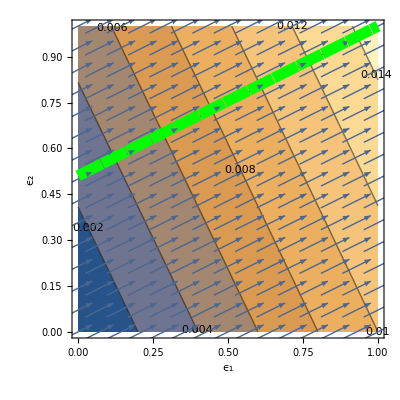
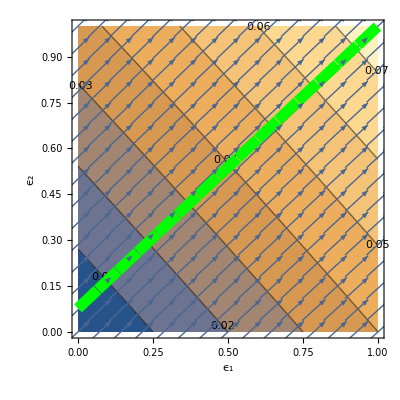
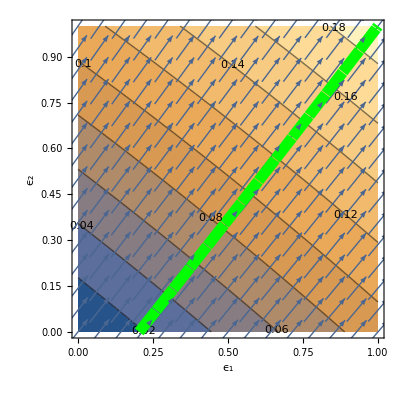
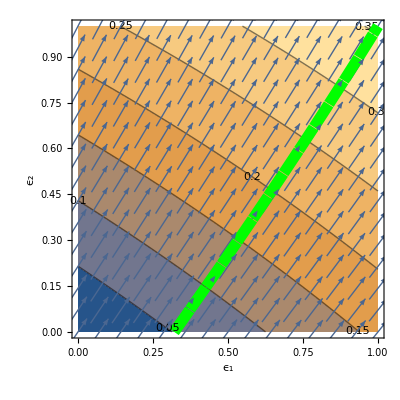
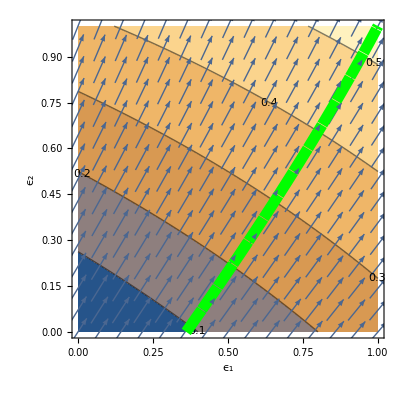
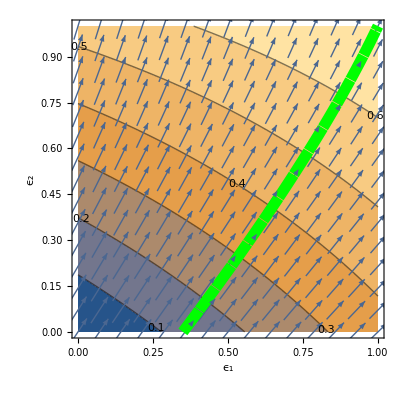
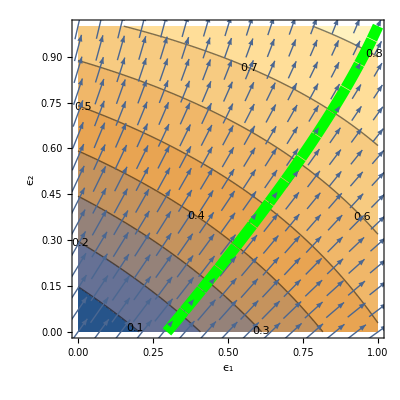
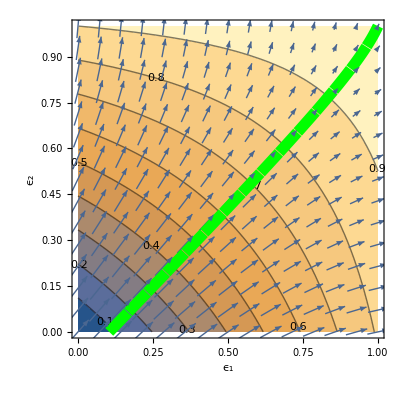
```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```